```mathematica
β[ω_,δ_,t_,ϵ_,m_]:=β[ω,δ,t,ϵ,m]=ReplacePart[(ω+ⅈ*δ-ϵ)IdentityMatrix[m],Join[Table[{i,i-1},{i,Range[2,m,1]}],Table[{i,i+1},{i,Range[1,m,1]}]]->-t]
```

```mathematica
T[t_,m_]:=T[t,m]=t*IdentityMatrix[m]
```

```mathematica
LEFT[ω_,δ_,t_,ϵ_,m_]:=LEFT[ω,δ,t,ϵ,m]=Module[{J=Inverse[β[ω,δ,t,ϵ,m]],A:=Inverse[β[ω,δ,t,ϵ,m]],T1:=T[t,m]},Do[J=Inverse[IdentityMatrix[m]-A.T1.J.T1].A,60000];J=J]
```

```mathematica
g[ω_,δ_,t_,ϵ_,m_]:= Inverse[β[ω,δ,t,ϵ,m]]
```

```mathematica
SR[ω_,δ_,t_,ϵ_,m_]:=Inverse[IdentityMatrix[m]-g[ω,δ,t,ϵ,m].T[t,m].LEFT[ω,δ,t,ϵ,m].T[t,m]].g[ω,δ,t,ϵ,m]
```

```mathematica
SL[ω_,δ_,t_,ϵ_,m_]:=Inverse[IdentityMatrix[m]-g[ω,δ,t,ϵ,m].T[t,m].LEFT[ω,δ,t,ϵ,m].T[t,m]].g[ω,δ,t,ϵ,m]
```

```mathematica
tr[0,0.0001,1,0,4]
```

4.

```mathematica
IL[ω_,δ_,t_,ϵ_,m_]:=Inverse[IdentityMatrix[m]-SL[ω,δ,t,ϵ,m].T[t,m].SR[ω,δ,t,ϵ,m].T[t,m]].SL[ω,δ,t,ϵ,m]
```

```mathematica
IR[ω_,δ_,t_,ϵ_,m_]:=Inverse[IdentityMatrix[m]-SR[ω,δ,t,ϵ,m].T[t,m].SL[ω,δ,t,ϵ,m].T[t,m]].SR[ω,δ,t,ϵ,m]
```

```mathematica
gdd[ω_,δ_,t_,ϵ_,m_]:= IL[ω,δ,t,ϵ,m]-ConjugateTranspose[IL[ω,δ,t,ϵ,m]]
```

```mathematica
grr[ω_,δ_,t_,ϵ_,m_]:= IR[ω,δ,t,ϵ,m]-ConjugateTranspose[IR[ω,δ,t,ϵ,m]]
```

```mathematica
Gnonlocal[ω_,δ_,t_,ϵ_,m_]:= SR[ω,δ,t,ϵ,m].T[t,m].IL[ω,δ,t,ϵ,m]
```

```mathematica
GNON[ω_,δ_,t_,ϵ_,m_]:= Gnonlocal[ω,δ,t,ϵ,m]-ConjugateTranspose[Gnonlocal[ω,δ,t,ϵ,m]]
```

```mathematica
tr[ω_,δ_,t_,ϵ_,m_]:= Abs[Tr[gdd[ω,δ,t,ϵ,m].T[t,m].grr[ω,δ,t,ϵ,m].T[t,m]-T[t,m].GNON[ω,δ,t,ϵ,m].T[t,m].GNON[ω,δ,t,ϵ,m]]]
```

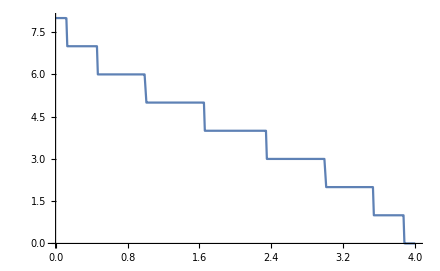

```mathematica
pris8=ListLinePlot[Table[{ω,Abs[tr[ω,0.0001,1,0,8]]},{ω,Range[0,4,0.01]}]]
```

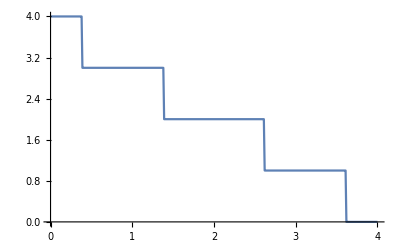

```mathematica
pris4=ListLinePlot[Table[{ω,Abs[tr[ω,0.0001,1,0,4]]},{ω,Range[0,4,0.01]}]]
```

```mathematica
Clear[SLLEAD,VLEAD]
```

```mathematica
SLLEAD1[ω_,δ_,t_,ϵ_]:=Module[{MAT=0*IdentityMatrix[8]},MAT[[1;;4,1;;4]]=SL[ω,δ,t,ϵ,4];MAT]
```

```mathematica
VLEAD1[t_]:=Module[{abc=0*IdentityMatrix[8]},abc[[1;;4,1;;4]]=T[t,4];abc]
```

```mathematica
SLLEAD2[ω_,δ_,t_,ϵ_]:=Module[{MAT=0*IdentityMatrix[8]},MAT[[5;;8,5;;8]]=SL[ω,δ,t,ϵ,4];MAT]
```

```mathematica
VLEAD2[t_]:=Module[{abc=0*IdentityMatrix[8]},abc[[5;;8,5;;8]]=T[t,4];abc]
```

```mathematica
deviceleft[ω_,δ_,t_,ϵ_,m_,ϵ1_,n_]:=Module[{Tin=T[t,m],μ1=RandomInteger[{1,m}], μ2=RandomInteger[{1,m}], μ3=RandomInteger[{1,m}], μ4=RandomInteger[{1,m}],μ5=RandomInteger[{1,m}], μ6=RandomInteger[{1,m}], μ7=RandomInteger[{1,m}],μ8=RandomInteger[{1,m}],μ9=RandomInteger[{1,m}], μ10=RandomInteger[{1,m}], μ11=RandomInteger[{1,m}],μ12=RandomInteger[{1,m}], μ13=RandomInteger[{1,m}],μ14=RandomInteger[{1,m}]},
imp1:=Inverse[Module[{κ=β[ω,δ,t,ϵ,m]},ReplacePart[κ,{{μ1,μ1}}->ω+ⅈ*0.0001-ϵ1]]];
imp2:=Inverse[Module[{κ=β[ω,δ,t,ϵ,m]},ReplacePart[κ,{{μ2,μ2}}->ω+ⅈ*0.0001-ϵ1]]];
imp3:=Inverse[Module[{κ=β[ω,δ,t,ϵ,m]},ReplacePart[κ,{{μ3,μ3}}->ω+ⅈ*0.0001-ϵ1]]];
imp4:=Inverse[Module[{κ=β[ω,δ,t,ϵ,m]},ReplacePart[κ,{{μ4,μ4}}->ω+ⅈ*0.0001-ϵ1]]];
imp5:=Inverse[Module[{κ=β[ω,δ,t,ϵ,m]},ReplacePart[κ,{{μ5,μ5}}->ω+ⅈ*0.0001-ϵ1]]];
imp6:=Inverse[Module[{κ=β[ω,δ,t,ϵ,m]},ReplacePart[κ,{{μ6,μ6}}->ω+ⅈ*0.0001-ϵ1]]];
imp7:=Inverse[Module[{κ=β[ω,δ,t,ϵ,m]},ReplacePart[κ,{{μ7,μ7}}->ω+ⅈ*0.0001-ϵ1]]];
imp8:=Inverse[Module[{κ=β[ω,δ,t,ϵ,m]},ReplacePart[κ,{{μ8,μ8}}->ω+ⅈ*0.0001-ϵ1]]];
imp9:=Inverse[Module[{κ=β[ω,δ,t,ϵ,m]},ReplacePart[κ,{{μ9,μ9}}->ω+ⅈ*0.0001-ϵ1]]];
imp10:=Inverse[Module[{κ=β[ω,δ,t,ϵ,m]},ReplacePart[κ,{{μ10,μ10}}->ω+ⅈ*0.0001-ϵ1]]];
imp11:=Inverse[Module[{κ=β[ω,δ,t,ϵ,m]},ReplacePart[κ,{{μ11,μ11}}->ω+ⅈ*0.0001-ϵ1]]];
imp12:=Inverse[Module[{κ=β[ω,δ,t,ϵ,m]},ReplacePart[κ,{{μ12,μ12}}->ω+ⅈ*0.0001-ϵ1]]];
imp13:=Inverse[Module[{κ=β[ω,δ,t,ϵ,m]},ReplacePart[κ,{{μ13,μ13}}->ω+ⅈ*0.0001-ϵ1]]];
imp14:=Inverse[Module[{κ=β[ω,δ,t,ϵ,m]},ReplacePart[κ,{{μ14,μ14}}->ω+ⅈ*0.0001-ϵ1]]];
imp:=Inverse[Module[{κ=β[ω,δ,t,ϵ,m]},ReplacePart[κ,{{1,1}}->ω+ⅈ*0.0001-0]]];
list={RandomSample[{imp1,imp2,imp3,imp4,imp5,imp6,imp7,imp8(*,imp9,imp10*)}]};
SLLEAD=Module[{MAT=0*IdentityMatrix[m]},MAT[[1;;4,1;;4]]=SL[ω,δ,t,ϵ,4];MAT];
VLEAD=Module[{abc=0*IdentityMatrix[m]},abc[[1;;4,1;;4]]=T[t,4];abc];
glead=Module[{xyz=0*IdentityMatrix[m]},xyz[[5;;8,5;;8]]=g[ω,δ,t,ϵ,4];xyz];
b=Module[{},
sl1=Inverse[IdentityMatrix[m]-list[[1,1]].ConjugateTranspose[VLEAD].SLLEAD.VLEAD].list[[1,1]];
sl2= Module[{J=sl1},Do[J=Inverse[IdentityMatrix[m]-list[[1,ζ]].ConjugateTranspose[T[t,m]].J.T[t,m]].list[[1,ζ]];,{ζ,2,n}];
 J=J](*
sl3=Inverse[IdentityMatrix[m]-glead.ConjugateTranspose[VLEAD].sl2.VLEAD].glead*)];
b]
```

```mathematica
Clear[deltae,list]
```

```mathematica
IR[ω_,δ_,t_,ϵ_,m_,ϵ1_,n_]:=Inverse[IdentityMatrix[8]-SLLEAD2[ω,δ,t,ϵ].VLEAD2[t].deviceleft[ω,δ,t,ϵ,m,ϵ1,n].VLEAD2[t]].SLLEAD2[ω,δ,t,ϵ]
```

```mathematica
IL[ω_,δ_,t_,ϵ_,m_,ϵ1_,n_]:= Inverse[IdentityMatrix[8]-deviceleft[ω,δ,t,ϵ,m,ϵ1,n].VLEAD2[t].SLLEAD2[ω,δ,t,ϵ].VLEAD2[t]].deviceleft[ω,δ,t,ϵ,m,ϵ1,n]
```

```mathematica
transmission[ω_,δ_,t_,ϵ_,m_,ϵ1_,n_]:=Module[{Il1=IL[ω,δ,t,ϵ,m,ϵ1,n],Ir1=IR[ω,δ,t,ϵ,m,ϵ1,n]},
gdd1:= Il1-ConjugateTranspose[Il1];grr1:= Ir1-ConjugateTranspose[Ir1];Gnonlocal1:= SLLEAD2[ω,δ,t,ϵ].VLEAD2[t].Il1;GNON1:= Gnonlocal1-ConjugateTranspose[Gnonlocal1];If[Abs[Tr[gdd1.VLEAD2[t].grr1.VLEAD2[t]-VLEAD2[t].GNON1.VLEAD2[t].GNON1]]>tr[ω,δ,t,ϵ,m],tr[ω,δ,t,ϵ,m],Abs[Tr[gdd1.VLEAD2[t].grr1.VLEAD2[t]-VLEAD2[t].GNON1.VLEAD2[t].GNON1]]]]
```

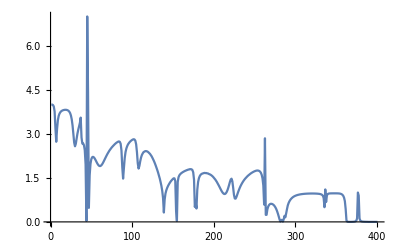

```mathematica
ListLinePlot[Table[transmission[ω,0.0001,1,0,8,0,7],{ω,Range[0,4,0.01]}]]
```